# Tracking evolution of domains during domain splitting

Here we analyze the coarsening process of mesh patterns in the switch+PMB Min system.

## Import data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

```mathematica
times=Join[{0},10^Range[0,6,0.1]];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-splitting1.txt","Comsol2DSweep"];
```

```mathematica
data=Partition[dataMesh["mde+me"],Length@times];
```

```mathematica
grid=dataMesh["Grid"];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-splitting2.txt","Comsol2DSweep"];
```

```mathematica
data=Join[data,Partition[dataMesh["mde+me"],Length@times]];
```

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinEmesh-splitting3.txt","Comsol2DSweep"];
```

```mathematica
data=Join[data,Partition[dataMesh["mde+me"],Length@times]];
```

MinD density for example plot

```mathematica
dataMesh=Import[NotebookDirectory[]<>"MinSwitchPMB-2Dflat-MinD-splitting1.txt","Comsol2DSweep"];
dataMinD=Partition[dataMesh["mde+md"],Length@times];
```

## Data visualization

```mathematica
Manipulate[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,{i,1,Length@data[[1]]},{sim,1,Length@data}]
```

```mathematica
Manipulate[Thinning[Binarize[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,0.1],Padding->1],{i,1,Length@times},{sim,1,Length@data}]
```

```mathematica
Manipulate[MorphologicalComponents[ImagePad[Thinning[Binarize[Image[data[[Floor@sim,Floor@i]]]//ImageAdjust,0.1],Padding->1],1]//ColorNegate,CornerNeighbors->False]//Colorize,{i,1,Length@times},{sim,1,Length@data}]
```

### Example patterns

```mathematica
colorMap={minD/1.5,minE,minE+minD/1.5/1.5};
```

Example bubbles labeled by boxes

```mathematica
ind=12;
times[[ind]]
Show[
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]})),
Graphics[{Red,
Rectangle[{50,300-65},{125,300-125}],
Blue,
Rectangle[{200,300-195},{270,300-270}],
Purple,
Rectangle[{135,300-75},{195,300-135}]}]
]
```

10.

-Graphics-

```mathematica
ind=32;
times[[ind]]
Show[
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]})),
Graphics[{Red,
Rectangle[{50,300-65},{125,300-125}],
Blue,
Rectangle[{200,300-195},{270,300-270}],
Purple,
Rectangle[{135,300-75},{195,300-135}]}]
]
```

1000.

-Graphics-

```mathematica
ind=42;
times[[ind]]
Show[
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]})),
Graphics[{Red,
Rectangle[{50,300-65},{125,300-125}],
Blue,
Rectangle[{200,300-195},{270,300-270}],
Purple,
Rectangle[{135,300-75},{195,300-135}]}]
]
```

10000.

-Graphics-

```mathematica
ind=49;
times[[ind]]
Show[
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1,ind]],dataMinD[[1,ind]]})),
Graphics[{Red,
Rectangle[{50,300-65},{125,300-125}],
Blue,
Rectangle[{200,300-195},{270,300-270}],
Purple,
Rectangle[{135,300-75},{195,300-135}]}]
]
```

50118.7

-Graphics-

## Measure domains

```mathematica
domains=Table[Table[Block[{
mesh=ImagePad[Thinning[Binarize[Image[frame]//ImageAdjust,0.1],Padding->1],1],
morphComps,
meas,
branchPoints,
cornerNumbers
},
morphComps=MorphologicalComponents[mesh//ColorNegate,CornerNeighbors->False];
meas=SortBy[ComponentMeasurements[morphComps,{"Centroid","Area","MaxPerimeterDistance","MaxCentroidDistance"}],Values[#][[2]]&][[;;-2]];
branchPoints=MorphologicalBranchPoints[mesh];
Select[Table[With[{mask=Dilation[Map[If[#==domain,1,0]&,morphComps,{2}],DiskMatrix[1]]},
{
Sequence@@(domain/.meas),
Total@Flatten[mask*ImageData[branchPoints]]
}
],
{domain,Keys@meas}],#[[2]]>10&]
],
{frame,sim}],{sim,data}];
```

Single example domains

```mathematica
Manipulate[MorphologicalComponents[ImagePad[Thinning[Binarize[Image[data[[1,Floor@i,65;;125,50;;125]]]//ImageAdjust,0.1],Padding->1],1]//ColorNegate,CornerNeighbors->False]//Colorize,{i,1,Length@data[[1]]}]
```

```mathematica
domainsSplit=Table[Block[{
mesh=ImagePad[Thinning[Binarize[Image[frame[[65;;125,50;;125]]]//ImageAdjust,0.1],Padding->1],1],
morphComps,
meas,
branchPoints,
cornerNumbers
},
morphComps=MorphologicalComponents[mesh//ColorNegate,CornerNeighbors->False];
meas=SortBy[ComponentMeasurements[morphComps,{"Centroid","Area","MaxPerimeterDistance","MaxCentroidDistance"}],Values[#][[2]]&][[;;-2]];
branchPoints=MorphologicalBranchPoints[mesh];
Select[Table[With[{mask=Dilation[Map[If[#==domain,1,0]&,morphComps,{2}],DiskMatrix[1]]},
{
Sequence@@(domain/.meas),
Total@Flatten[mask*ImageData[branchPoints]]
}
],
{domain,Keys@meas}],#[[2]]>10&]
],
{frame,data[[1]]}];
```

```mathematica
Manipulate[MorphologicalComponents[ImagePad[Thinning[Binarize[Image[data[[1,Floor@i,195;;270,200;;270]]]//ImageAdjust,0.1],Padding->1],1]//ColorNegate,CornerNeighbors->False]//Colorize,{i,1,Length@data[[1]]}]
```

```mathematica
domainsSplitLate=Table[Block[{
mesh=ImagePad[Thinning[Binarize[Image[frame[[195;;270,200;;270]]]//ImageAdjust,0.1],Padding->1],1],
morphComps,
meas,
branchPoints,
cornerNumbers
},
morphComps=MorphologicalComponents[mesh//ColorNegate,CornerNeighbors->False];
meas=SortBy[ComponentMeasurements[morphComps,{"Centroid","Area","MaxPerimeterDistance","MaxCentroidDistance"}],Values[#][[2]]&][[;;-2]];
branchPoints=MorphologicalBranchPoints[mesh];
Select[Table[With[{mask=Dilation[Map[If[#==domain,1,0]&,morphComps,{2}],DiskMatrix[1]]},
{
Sequence@@(domain/.meas),
Total@Flatten[mask*ImageData[branchPoints]]
}
],
{domain,Keys@meas}],#[[2]]>10&]
],
{frame,data[[1]]}];
```

```mathematica
Manipulate[MorphologicalComponents[ImagePad[Thinning[Binarize[Image[data[[1,Floor@i,75;;135,135;;195]]]//ImageAdjust,0.1],Padding->1],1]//ColorNegate,CornerNeighbors->False]//Colorize,{i,1,Length@data[[1]]}]
```

```mathematica
domainsNoSplit=Table[Block[{
mesh=ImagePad[Thinning[Binarize[Image[frame[[75;;135,135;;195]]]//ImageAdjust,0.1],Padding->1],1],
morphComps,
meas,
branchPoints,
cornerNumbers
},
morphComps=MorphologicalComponents[mesh//ColorNegate,CornerNeighbors->False];
meas=SortBy[ComponentMeasurements[morphComps,{"Centroid","Area","MaxPerimeterDistance","MaxCentroidDistance"}],Values[#][[2]]&][[;;-2]];
branchPoints=MorphologicalBranchPoints[mesh];
Select[Table[With[{mask=Dilation[Map[If[#==domain,1,0]&,morphComps,{2}],DiskMatrix[1]]},
{
Sequence@@(domain/.meas),
Total@Flatten[mask*ImageData[branchPoints]]
}
],
{domain,Keys@meas}],#[[2]]>10&]
],
{frame,data[[1]]}];
```

## Track domains

#### All domains

Collect domains found in each frame into time tracks of single domains moving around in the system

```mathematica
domainTracksNC=Table[{{times[[1]],#}}&/@(dom[[1]]),{dom,domains}];
Monitor[Do[Do[Block[{
doms=domains[[simInd,i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTracksNC[[simInd]]]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTracksNC[[simInd]]};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&distancesSorted[[2,2]]>20,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[domainTracksNC[[simInd,distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTracksNC[[simInd]],{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}],{simInd,Length@data}];,{simInd,i}]
domainTracksNC=Flatten[domainTracksNC,1];
```

```mathematica
domainTracksJump=Select[domainTracksNC,Max[-Differences[#[[All,2,2]]]/#[[2;;,2,2]]]>1/2&];
```

```mathematica
domainTracksNoJump=Select[domainTracksNC,Max[-Differences[#[[All,2,2]]]/#[[2;;,2,2]]]<=1/2&];
```

#### Example domains

```mathematica
domainTrackSplit={{times[[1]],#}}&/@domainsSplit[[1]];
Do[Block[{
doms=domainsSplit[[i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTrackSplit]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTrackSplit};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&(distancesSorted[[1,2]]==distancesSorted[[-1,2]]||distancesSorted[[2,2]]>20),(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[domainTrackSplit[[distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTrackSplit,{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}];
```

```mathematica
domainTrackSplitLate={{times[[1]],#}}&/@domainsSplitLate[[1]];
Do[Block[{
doms=domainsSplitLate[[i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTrackSplitLate]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTrackSplitLate};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&(distancesSorted[[1,2]]==distancesSorted[[-1,2]]||distancesSorted[[2,2]]>20),(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[domainTrackSplitLate[[distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTrackSplitLate,{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}];
```

```mathematica
domainTrackNoSplit={{times[[1]],#}}&/@domainsNoSplit[[1]];
Do[Block[{
doms=domainsNoSplit[[i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTrackNoSplit]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTrackNoSplit};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&(distancesSorted[[1,2]]==distancesSorted[[-1,2]]||distancesSorted[[2,2]]>20),(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[domainTrackNoSplit[[distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTrackNoSplit,{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}];
```

### Analysis

Factors (100/300) to measure lengths in simulation units;
Moreover, areas are scaled by a factor 2 in the simultion.

#### Initial distribution

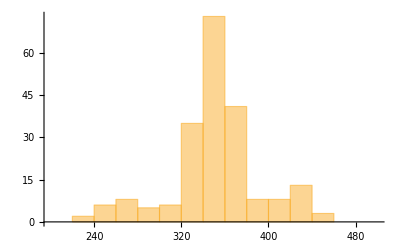

```mathematica
Histogram[(100/300)^2*2{
Flatten[domains[[All,1]],1][[All,2]]
},{200,500,20}]
```

#### Final distribution

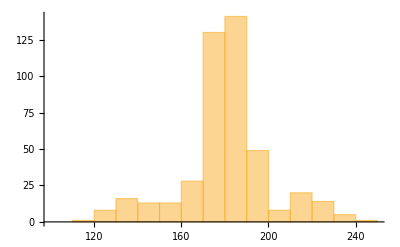

```mathematica
Histogram[(100/300)^2*2{
Flatten[domains[[All,-1]],1][[All,2]]
},{100,250,10}]
```

#### Time evolution of domain sizes

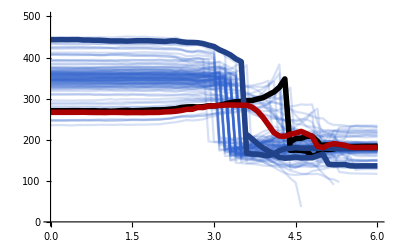

```mathematica
Show[
ListLinePlot[({Log10@#[[1]],(100/300)^2*2*#[[2,2]]}&/@#)&/@Select[domainTracksNC,#[[1,1]]==0&][[;;;;2]],PlotStyle->{RGBColor[{49,99,206,50}/255]},PlotRange->{0,500}],
ListLinePlot[
({Log10@#[[1]],(100/300)^2*2*#[[2,2]]}&/@#)&/@domainTrackSplitLate
,PlotStyle->{{Thickness[0.01],Black}},PlotRange->All],
ListLinePlot[
({Log10@#[[1]],(100/300)^2*2*#[[2,2]]}&/@#)&/@domainTrackSplit
,PlotStyle->{{Thickness[0.01],Darker@RGBColor[{49,99,206}/255]}},PlotRange->All],
ListLinePlot[
({Log10@#[[1]],(100/300)^2*2*#[[2,2]]}&/@#)&/@domainTrackNoSplit
,PlotStyle->{{Thickness[0.01],Darker@Red}},PlotRange->All]
]
```

### Size distribution of splitting domains

```mathematica
splitList=HistogramList[(100/300)^2*2Max[#[[All,2,2]]]&/@Select[domainTracksJump,#[[1,1]]==0&],{270,460,10}]
```

{{270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460},{0,1,0,1,2,6,15,38,37,34,17,8,4,7,1,7,6,2,1}}

```mathematica
allList=HistogramList[(100/300)^2*2Max[#[[All,2,2]]]&/@Select[domainTracksNC,#[[1,1]]==0&],{270,460,10}]
```

{{270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460},{3,4,3,2,4,11,18,39,37,34,17,8,4,7,1,7,6,2,1}}

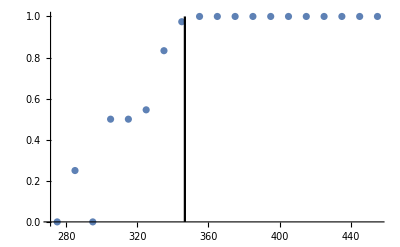

```mathematica
Show[
ListPlot[Transpose[{MovingAverage[allList[[1]],2],splitList[[2]]/allList[[2]]}]],
ListLinePlot[{{splittingArea,0},{splittingArea,1}},PlotStyle->Black]
]
```

## Splitting threshold from single domain simulation

Data from Comsol simulation of a single spherical domain that is a adiabatically enlarged.

```mathematica
splittingArea=Pi 5^2 (1+(4.415*10^5-10^5)/10^5)
```

346.753